Погрешность приближения равна: 8.93146×10^-6

Количество многочленов Лежандра в семействе равно: 9

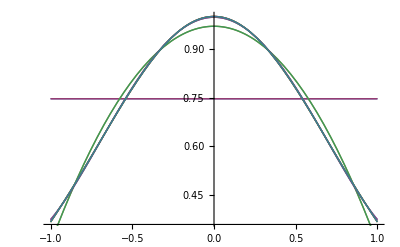

```mathematica
(*Зададим данную функцию*)
f[x_]=Exp[-x^2];
(*Зададим отрезок аппрокисмации*)
a=-1;
b=1;
(*Зададим точность приближения*)
eps=10^(-5);
(*Зададим начальную погрешность*)
r=eps+1;
(*Зададим счетчик степеней многочленов Лежандра*)
n=0;
(*Зададим переменную для хранения последовательности приближений*)
Phi=List[];
While[r≥eps,
(*Зададим семейство многочленов Лежандра*)
F=Table[LegendreP[k,x],{k,0,n}];
(*Зададим коэффициенты обобщенного многочлена наилучших среднеквадратических приближений*)
K=Array[k,n+1];
(*Построим среднеквадратическое отклонение построенного семейства от заданной функции*)
S=Sqrt[Integrate[(f[x]-K.F)^2,{x,a,b}]];
(*Найдем наименьшее значение среднеквадратического отклонения*)
M=NMinimize[S,K];
(*Построим коэффициенты обобщенного многочлена, наилучшим образом приближающего данную функцию*)
K=Table[k[i]/.M[[2,i]],{i,1,n+1}];
(*Добавим очередной обобщенный многочлен в последовательность*)
AppendTo[Phi,K.F];
(*Найдем погрешность приближения*)
r=Sqrt[NIntegrate[(f[x]-K.F)^2,{x,a,b}]];
n=n+1;
];
Print["Погрешность приближения равна: ",r]
Print["Количество многочленов Лежандра в семействе равно: ",n]
(*Построим график данной функции и последовательности приближений в одной системе координат*)
G=Plot[f[x],{x,a,b},PlotStyle->Red];
GPhi=Plot[Phi,{x,a,b}];
Show[G,GPhi]
```

```mathematica
Animate[Show[G,Plot[Phi[[i]],{x,a,b}]],{i,1,n,1},AnimationRunning->False]
```